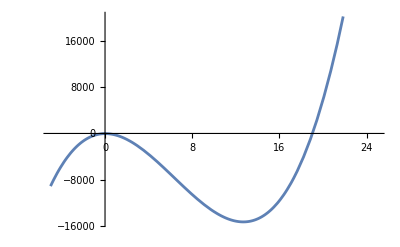

```mathematica
(*
ЗАДАНИЕ 1
Отделите графически корни алгебраического уравнения f (x)=0 с помощью функ-ции Plot.
Найдите один из них (нецелый) с точностью ε=10^(−3) методом хорд.Укажите
потребовавшееся число итераций.Проиллюстрируйте графически нахождение первых
двух приближений (постройте график функции и хорды).
1.1.f(x)=15x^3−86x^2+11x−28.
*)
f[x_]:=15 x^3-286x^2+11 x-28
Plot[f[x],{x,-5,25}]
```

```mathematica
chordMethod[f_,a_,b_,eps_]:=Module[{x0=a,x1=b,x2,ll,iter=0,history={}},
While[True,x2=x1-f[x1]*(x1-x0)/(f[x1]-f[x0]);
iter++;
ll = (x2-x1)^2/Abs[x2+x0-2*x1];
AppendTo[history,{iter,N[x2,6],N[f[x2],6],N[ll,6]}];
If[ll<eps,Break[]];
x0=x1;
x1=x2;];
{N[x2,6],iter,history}]
```

Найденный корень: 19.0333

Потребовавшееся число итераций: 4

Таблица итераций:

№ | x_n | f(x_n) | ll
1 | 18.7561 | -1460.27 | 1.45262
2 | 18.9624 | -381.976 | 0.0123262
3 | 19.0354 | 11.5329 | 0.0400732
4 | 19.0333 | -0.0864541 | 0.0000609603

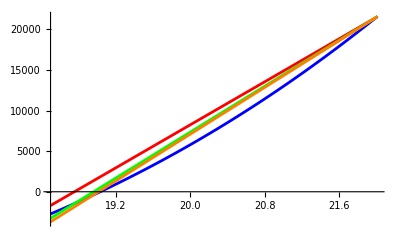

Найденный корень: 3.66664

Потребовавшееся число итераций: 5

Таблица итераций:

1 | 3.41892 | -37.9942 | 0.21356
2 | 3.59697 | -12.7427 | 0.0417624
3 | 3.68682 | 4.00309 | 0.0915319
4 | 3.66535 | -0.257251 | 0.00414399
5 | 3.66664 | -0.00465082 | 0.

```mathematica
result=chordMethod[f,18,22,10^-3];
Print["Найденный корень: ",result[[1]]];
Print["Потребовавшееся число итераций: ",result[[2]]];
Print["Таблица итераций:"];
Print[TableForm[result[[3]],TableHeadings->{None,{"№","x_n","f(x_n)","ll"}}]];


chord[x_,a_,b_]:=f[a]+(f[b]-f[a])/(b-a)*(x-a)
chord1[x_]:=chord[x,18,22];
chord2[x_]:=chord[x,result[[3,1,2]],22];
chord3[x_]:=chord[x,result[[3,2,2]],22];

Plot[{f[x],chord1[x],chord2[x],chord3[x]},{x,18.5,22.01},PlotStyle->{Blue,Red,Green,Orange}]
```

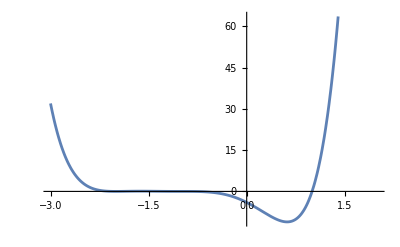

```mathematica
(*
ЗАДАНИЕ 2: 
Отделите графически и найдите с помощью функций Solve,NSolve,Roots,FindRoot
корни алгебраического уравнения f(x)=0. Разложите многочлен f (x) на множители, используя функцию Factor.
2.1.f (x)=x^6+6x^5+12x^4+6x^3−9x^2−12x−4.
*)
f2[x_]:=x^6+6x^5+12x^4+6x^3-9x^2-12x-4;
Plot[f2[x],{x,-3,2}]
```

```mathematica
Solve[f2[x]==0, x]
NSolve[f2[x]==0, x]
Roots[f2[x] ==0, x]
FindRoot[f2[x]==0,{x,-1.8}]
```

{{x→-2},{x→-2},{x→-1},{x→-1},{x→-1},{x→1}}

{{x→-2.},{x→-2.},{x→-1.},{x→-1.},{x→-1.},{x→1.}}

x==-2||x==-2||x==-1||x==-1||x==-1||x==1

{x→-2.}

```mathematica
Factor[f2[x]]
```

(-1+x) (1+x)^3 (2+x)^2

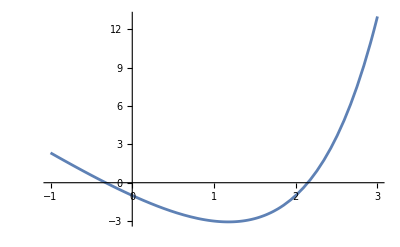

```mathematica
(*
3. Отделите графически корни трансцендентного уравнения с помощью функции Plot.
Найдите один из них с точностью ε=10^(−3):
а) методом Ньютона;
	б) методом секущих.
	Укажите потребовавшееся число итераций.
3.1.3^x=4x+2.
*)
f3[x_]:=3^(x)-4x-2;
Plot[f3[x],{x,-1,3}]
```

```mathematica
df3[x_]:=D[f3[t],t]/. t->x;
d2f3[x_]:=D[f3[t],{t,2}]/. t->x;
(*а) Метод Ньютона*)
newtonMethod[f_,df_,a_,eps_] := Module[{x1=a,x2,iter=0, history={}} ,
While[True, x2 = x1-f[x1]/df[x1];
iter++;
AppendTo[history,{iter,N[x2,6],N[f[x2],6],N[Abs[x2-x1],6]}];
If[Abs[x2-x1]<eps, Break[]];
x1=x2;
 ];
{N[x2,6],iter,history}]
(*Этим методом будем искать корень находящийся в промежутке (-1,0)*)
```

SetDelayed::write: Tag Plus in (-4+3^t Log[3])[x_] is Protected.

SetDelayed::write: Tag Times in (3^t Log[3]^2)[x_] is Protected.

```mathematica
N[f3[-1]*d2f3[-1],6]
N[f3[0]*d2f3[0],6]
```

0.938738

-1.20695

```mathematica
(*Значит нужно брать границу -1*)
result = newtonMethod[f3,df3,-1,10^(-3)];
Print["Найденный корень: ",result[[1]]];
Print["Потребовавшееся число итераций: ",result[[2]]];
Print["Таблица итераций:"];
Print[TableForm[result[[3]],TableHeadings->{None,{"№","x_n","f(x_n)","loss"}}]]
```

Найденный корень: -0.325081

Потребовавшееся число итераций: 3

Таблица итераций:

№ | x_n | f(x_n) | loss
1 | -0.35788 | 0.106433 | 0.64212
2 | -0.325217 | 0.000439768 | 0.0326628
3 | -0.325081 | 7.8193×10^-9 | 0.00013609

```mathematica
(*б) Метод секущих*)
secushMethod[f_,a_,b_,eps_] := Module[{x0=b,x1=a,x2,iter=0, history={}} ,
While[True, x2 = x1-f[x1]*(x1-x0)/(f[x1]-f[x0]);
iter++;
AppendTo[history,{iter,N[x2,6],N[f[x2],6],N[Abs[x2-x1],6]}];
If[Abs[x2-x1]<eps, Break[]];
x0=x1;
x1=x2;
 ];
{N[x2,6],iter,history}]
```

```mathematica
result = secushMethod[f3,2,3,10^(-3)];
Print["Найденный корень: ",result[[1]]];
Print["Потребовавшееся число итераций: ",result[[2]]];
Print["Таблица итераций:"];
Print[TableForm[result[[3]],TableHeadings->{None,{"№","x_n","f(x_n)","loss"}}]]
```

Найденный корень: 2.14838

Потребовавшееся число итераций: 4

Таблица итераций:

№ | x_n | f(x_n) | loss
1 | 2.07143 | -0.551014 | 0.0714286
2 | 2.15909 | 0.0824671 | 0.08766
3 | 2.14768 | -0.00542909 | 0.0114117
4 | 2.14838 | -0.0000484233 | 0.000704864

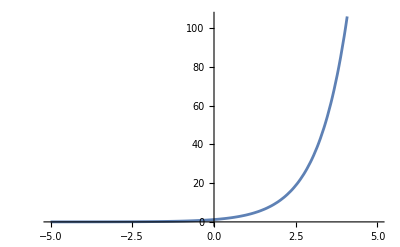

```mathematica
(*4. Приведите уравнение (3.1–3.16) к виду,пригодному для итераций.Найдите его
корни методом простых итераций с точностью ε=10^(−3). Укажите потребовавшееся
число итераций.*)
(*Приведем функцию методом релаксации*)
Plot[d2f3/.t->x,{x,-5,5}]
```

```mathematica
(*получается максимальным значением на промежутке будет в точке 0*)
ClearAll[f3,df3,d2f3,Phi,dPhi,lambda,q]
f3[x_]=3^x-4 x-2;
df3[x_]=D[f3[x],x];
d2f3[x_]=D[f3[x],{x,2}];

lambda=1/df3[0];
Phi[x_]=x-lambda*f3[x];
dPhi[x_]=D[Phi[x],x];
lambda=1/df3[0];
Phi[x_]=x-lambda*f3[x];
dPhi[x_]=D[Phi[t],t]/. t->x;
q=NMaximize[{Abs[dPhi[x]],-1<=x<=0},x][[1]]
```

0.252434

```mathematica
iterationMethod[f_,phi_,a_,eps_,q_]:=Module[{x1=a,x2,iter,history={},d0},x2=phi[x1];
d0=Abs[x2-x1];iter=1;
history={{iter,N[x2,6],N[f[x2],6],N[q^iter/(1-q)*d0,6]}};
While[q^iter/(1-q)*d0>=eps,x1=x2;x2=phi[x1];iter++;
AppendTo[history,{iter,N[x2,6],N[f[x2],6],N[q^iter/(1-q)*d0,6]}];];
{N[x2,6],iter,history}]

result=iterationMethod[f3,Phi,-1,10^-3,q]
```

{-0.325083,6,{{1,-0.195787,-0.410386,0.271562},{2,-0.337232,0.0393254,0.0685514},{3,-0.323678,-0.00453323,0.0173047},{4,-0.32524,0.000514689,0.00436829},{5,-0.325063,-0.0000585399,0.0011027},{6,-0.325083,6.65689×10^-6,0.000278359}}}

```mathematica
Print["Найденный корень: ",result[[1]]];
Print["Потребовавшееся число итераций: ",result[[2]]];
Print["Таблица итераций:"];
Print[TableForm[result[[3]],TableHeadings->{None,{"№","x_n","f(x_n)","loss"}}]]
```

Найденный корень: -0.325083

Потребовавшееся число итераций: 6

Таблица итераций:

№ | x_n | f(x_n) | loss
1 | -0.195787 | -0.410386 | 0.271562
2 | -0.337232 | 0.0393254 | 0.0685514
3 | -0.323678 | -0.00453323 | 0.0173047
4 | -0.32524 | 0.000514689 | 0.00436829
5 | -0.325063 | -0.0000585399 | 0.0011027
6 | -0.325083 | 6.65689×10^-6 | 0.000278359

```mathematica
(*
ЗАДАНИЕ 5
Решите уравнение (3.1–3.16) с помощью функций Solve,NSolve,FindRoot.
*)
Solve[f3[x]==0,x]
NSolve[f3[x]==0,x]
FindRoot[f3[x]==0,{x, 2}]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{x→(-Log[3]-2 ProductLog[-Log[3]/(4 √3)])/(2 Log[3])},{x→(-Log[3]-2 ProductLog[-1,-Log[3]/(4 √3)])/(2 Log[3])}}

{{x→-0.325081},{x→3.1091-6.6992 ⅈ},{x→3.1091+6.6992 ⅈ},{x→3.61294+12.5806 ⅈ},{x→3.9372+18.3717 ⅈ},{x→4.17643+24.1324 ⅈ},{x→4.36599+29.8789 ⅈ},{x→4.52296+35.6175 ⅈ},{x→4.65689+41.3513 ⅈ},{x→4.77367+47.0819 ⅈ},{x→4.8772+52.8103 ⅈ},{x→4.97018+58.537 ⅈ},{x→6.14241-213.012 ⅈ},{x→2.14839},{x→5.05455+64.2625 ⅈ},{x→5.13178+69.9871 ⅈ}}

{x→2.14839}

```mathematica
(*
ЗАДАНИЕ 6
Дана система двух нелинейных уравнений f (x,y)=0,g(x,y)=0. Используя сред-ства пакета Mathematica,изобразите на одном чертеже кривые f (x,y)=0 и g(x,y)=0,и решите данную систему.
6.16 f(x,y): (y+3)^2=(x^3−4x^2+4x)/(4−x)
	  g(x,y): (x^2+y^2+y)^2=30(x^2+y^2)
*)
f6[x_,y_]:=(y+3)^2-(x^3-4 x^2+4 x)/(4-x)
g6[x_,y_]:=(x^2+y^2+y)^2-30 (x^2+y^2)
ContourPlot[{f6[x,y],g6[x,y]},{x,-5,5},{y,-10,5},Contours->{0},ContourStyle->{Blue,Red}]
```

-Graphics-